Exercisi 0a

```mathematica
N[∑_(n=1)^2 1/n^2]
```

```mathematica
1.25
N[∑_(n=1)^10 1/n^2]
```

1.25

```mathematica
1.5497677311665408
N[∑_(n=1)^100 1/n^2]
```

1.54977

```mathematica
1.6349839001848927
N[∑_(n=1)^1000 1/n^2]
```

1.63498

```mathematica
1.64393456668156
∑_(n=1)^Infinity 1/n^2
```

1.64393

π^2/6

Exercisi 0b

```mathematica
∑_(n=1)^100 1/n
```

14466636279520351160221518043104131447711/2788815009188499086581352357412492142272

```mathematica
N[%]
```

5.18738

Exercisi 1

```mathematica
∑_(k=1)^n (2k-1)
```

n^2

Exercisi 2

```mathematica
∑_(n=1)^Infinity (-1)^(n+1)/n^4
```

(7 π^4)/720

```mathematica
N[%,20]
```

0.94703282949724591758

```mathematica
∑_(n=1)^50 (-1)^(n+1)/n^4
```

17470536703024220936994645310482948982134539259776946224703621068376366744877866434243/18447658387025422739514525102807080738504090416169831450549480686220672755384320000000

```mathematica
N[%,20]
```

0.947033

```mathematica
NumberForm[0.9470327526940532,16]
```

0.947032752694053

Exercisi 3

```mathematica
Simplify[n/(2n+1)-(n-1)/(2*(n-1)+1)]
```

1/(-1+4 n^2)

```mathematica
Limit[n/(2n+1),n->Infinity]
```

1/2

Exercisi 4

```mathematica
∑_(n=1)^Infinity (-1)^(n+1)/(n*(2^n))
```

Log[3/2]

```mathematica
N[Log[3/2]]
```

0.405465

```mathematica
Reduce[1/((n+1)*(2^(n+1)))<10^-5]
```

n<-1||n>(-Log[2]+ProductLog[100000 Log[2]])/Log[2]

```mathematica
N[%,10]
```

n<-1.||n>11.91829654

```mathematica
∑_(n=1)^12 (-1)^(n+1)/(n*(2^n))
```

23018117/56770560

```mathematica
N[23018117/56770560]
```

0.405459

Polinomi de Taylor pruebas libreta.

```mathematica
f[x_] = Log[x]
```

Log[x]

```mathematica
P[x_]=f[2]+f'[2]*(x-2)
```

1/2 (-2+x)+Log[2]

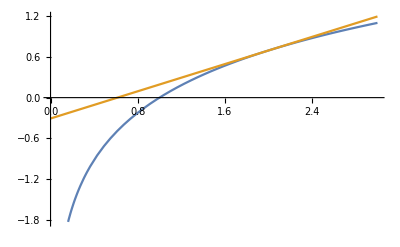

```mathematica
Plot[{Log[x],P[x]},{x,0,3}]
```

```mathematica
P[x_]=Normal[Series[f[x],{x,2,10}]]
```

1/2 (-2+x)-1/8 (-2+x)^2+1/24 (-2+x)^3-1/64 (-2+x)^4+1/160 (-2+x)^5-1/384 (-2+x)^6+1/896 (-2+x)^7-(-2+x)^8/2048+(-2+x)^9/4608-(-2+x)^10/10240+Log[2]

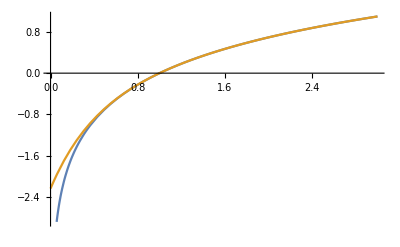

```mathematica
Plot[{Log[x],P[x]},{x,0,3}]
```

```mathematica
P[x_]=Normal[Series[f[x],{x,2,75}]]
```

1/2 (-2+x)-1/8 (-2+x)^2+1/24 (-2+x)^3-1/64 (-2+x)^4+1/160 (-2+x)^5-1/384 (-2+x)^6+1/896 (-2+x)^7-(-2+x)^8/2048+(-2+x)^9/4608-(-2+x)^10/10240+(-2+x)^11/22528-(-2+x)^12/49152+(-2+x)^13/106496-(-2+x)^14/229376+(-2+x)^15/491520-(-2+x)^16/1048576+(-2+x)^17/2228224-(-2+x)^18/4718592+(-2+x)^19/9961472-(-2+x)^20/20971520+(-2+x)^21/44040192-(-2+x)^22/92274688+(-2+x)^23/192937984-(-2+x)^24/402653184+(-2+x)^25/838860800-(-2+x)^26/1744830464+(-2+x)^27/3623878656-(-2+x)^28/7516192768+(-2+x)^29/15569256448-(-2+x)^30/32212254720+(-2+x)^31/66571993088-(-2+x)^32/137438953472+(-2+x)^33/283467841536-(-2+x)^34/584115552256+(-2+x)^35/1202590842880-(-2+x)^36/2473901162496+(-2+x)^37/5085241278464-(-2+x)^38/10445360463872+(-2+x)^39/21440476741632-(-2+x)^40/43980465111040+(-2+x)^41/90159953477632-(-2+x)^42/184717953466368+(-2+x)^43/378231999954944-(-2+x)^44/774056185954304+(-2+x)^45/1583296743997440-(-2+x)^46/3236962232172544+(-2+x)^47/6614661952700416-(-2+x)^48/13510798882111488+(-2+x)^49/27584547717644288-(-2+x)^50/56294995342131200+(-2+x)^51/114841790497947648-(-2+x)^52/234187180623265792+(-2+x)^53/477381560501272576-(-2+x)^54/972777519512027136+(-2+x)^55/1981583836043018240-(-2+x)^56/4035225266123964416+(-2+x)^57/8214565720323784704-(-2+x)^58/16717361816799281152+(-2+x)^59/34011184385901985792-(-2+x)^60/69175290276410818560+(-2+x)^61/140656423562035331072-(-2+x)^62/285924533142498050048+(-2+x)^63/581072438321850875904-(-2+x)^64/1180591620717411303424+(-2+x)^65/2398076729582241710080-(-2+x)^66/4869940435459321626624+(-2+x)^67/9887454823508319666176-(-2+x)^68/20070057552195992158208+(-2+x)^69/40730410914750689968128-(-2+x)^70/82641413450218791239680+(-2+x)^71/167644010141872405086208-(-2+x)^72/340010386766614455386112+(-2+x)^73/689465506498968201199616-(-2+x)^74/1397820478929414983254016+(-2+x)^75/2833419889721787128217600+Log[2]

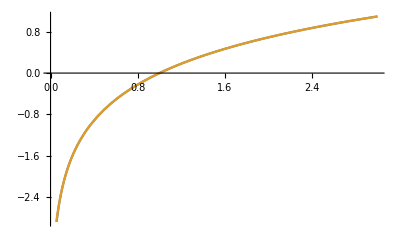

```mathematica
Plot[{Log[x],P[x]},{x,0,3}]
```

Exercisi 5

Exercisi 6

```mathematica
fsdfsdf
```